1.

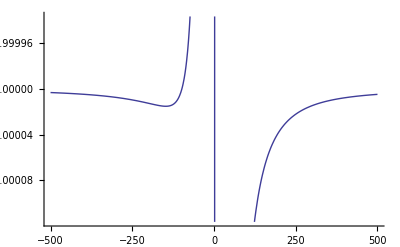

```mathematica
Plot[{(-30 x^3-3x+7+ⅇ^(-.001x))/(3 x^3-27-3 ⅇ^(-.001x))},{x, -500, 500} ]
```

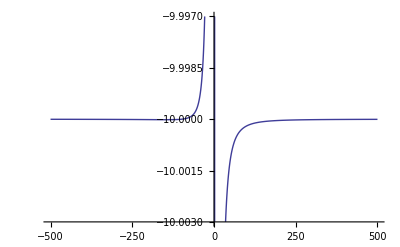

```mathematica
Plot[{(-30 x^3-3x+7+ⅇ^(-.001x))/(3 x^3-27-3 ⅇ^(-.001x))},{x, -500, 500}, {PlotRange->{-10.003, -9.997}} ]
```

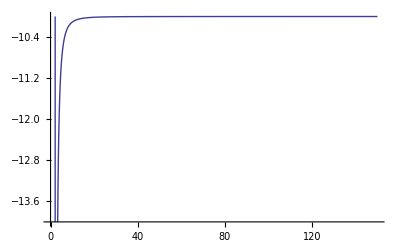

```mathematica
Plot[{(-30 x^3-3x+7+ⅇ^(-.001x))/(3 x^3-27-3 ⅇ^(-.001x))},{x, 0,150} , {PlotRange->{-14, -9.999}}]
```

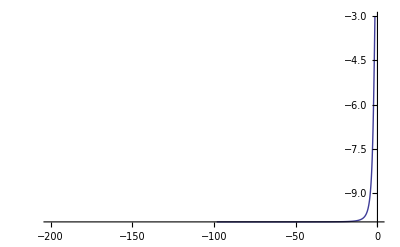

```mathematica
Plot[{(-30 x^3-3x+7+ⅇ^(-.001x))/(3 x^3-27-3 ⅇ^(-.001x))},{x, -200,0} , {PlotRange->{-10, -3}}]
```

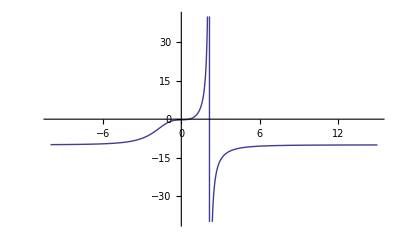

```mathematica
Plot[{(-30 x^3-3x+7+ⅇ^(-.001x))/(3 x^3-27-3 ⅇ^(-.001x))},{x, -10, 15}, {PlotRange->{-40, 40}} ]
```

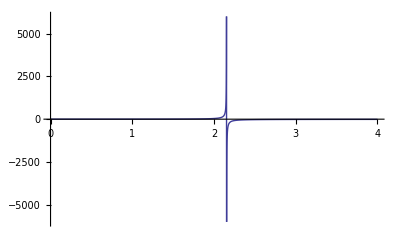

```mathematica
Plot[{(-30 x^3-3x+7+ⅇ^(-.001x))/(3 x^3-27-3 ⅇ^(-.001x))},{x, 0, 4}, {PlotRange->{-6000, 6000}} ]
```

2.

```mathematica
Plot[{g(x)=x^5-302 x^3+893 x^2+1208x-3588 }, {x, -5000, 5000}]
```

-Graphics-

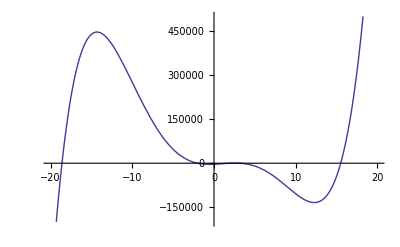

```mathematica
Plot[x^5-302 x^3+893 x^2+1208x-3588,{x,-20,20}, PlotRange -> {-2*10^5, 5*10^5 }]
```

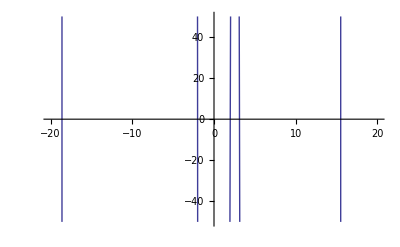

```mathematica
Plot[{g(x)=x^5-302 x^3+893 x^2+1208x-3588 }, {x, -20, 20}, PlotRange->{-50, 50}]
```

These graphs gives an overview of the function. We know that we have shown all of the significant parts because the polynomial is of degree five, so it can have at most five changes in direction, 5 zeros, and 5-1==4 relative minima or maxima. We have found all of them.

```mathematica
Limit[x^5-302 x^3+893 x^2+1208x-3588,x->-∞]
Limit[x^5-302 x^3+893 x^2+1208x-3588,x->∞]
```

-∞

∞

End Behavior: As x goes to negative infinity (the left), y goes to negative infinity (down). As x goes to positive infinity (the right), y goes to positive infinity (up). So, there are no horizontal asymptotes.

```mathematica
FindRoot[x^5-302 x^3+893 x^2+1208x-3588, {x, -19}]
FindRoot[x^5-302 x^3+893 x^2+1208x-3588, {x, 16}]
```

{x→-18.6}

{x→15.5027}

There are two zeros at -18.6 and about 15.5.

```mathematica
FindMaximum[x^5-302 x^3+893 x^2+1208x-3588, {x,-14}]
FindMinimum[x^5-302 x^3+893 x^2+1208x-3588, {x,12}]
```

{446891.,{x→-14.3168}}

{-134088.,{x→12.2668}}

There is a minimim at about (12.3, -134088) and a maximum at about (-14.3, 446891).

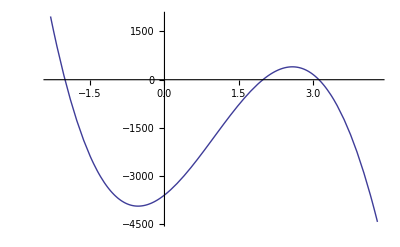

```mathematica
Plot[x^5-302 x^3+893 x^2+1208x-3588, {x, -2.3, 4.3}]
```

This graph shows a close-up of the function so the maxima and mimima are apparent.

```mathematica
FindMaximum[x^5-302 x^3+893 x^2+1208x-3588, {x, 2.6}]
FindMinimum[x^5-302 x^3+893 x^2+1208x-3588, {x, -.6}]
```

{400.727,{x→2.58264}}

{-3932.49,{x→-0.532666}}

There is a relative minimum at about (-.532, -3932.5) and a relative maximum at (2.58, 400.73).

```mathematica
z=0;
Solve[z^5-302 z^3+893 z^2+1208z-3588==y, y]
```

{{y→-3588}}

There is a y-intercept at about (0, -3588). This makes sense because the constant in the function is -3588.

There are no asymptotes on the graph. The function is a polynomial and thus is continuous for all real numbers.

3.

```mathematica
Plot[{h(x)=ⅇ^(2x)-4 ⅇ^x+2  }, {x, -100, 100}]
```

-Graphics-

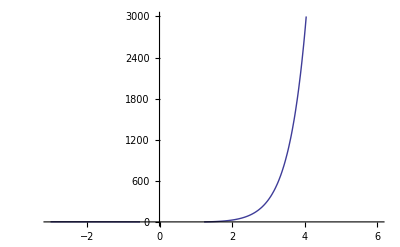

```mathematica
Plot[ⅇ^(2x)-4 ⅇ^x+2, {x, -3, 6}, PlotRange->{0, 3000}]
```

These graphs show the overview of the function.

```mathematica
Limit[ⅇ^(2x)-4 ⅇ^x+2,x->∞]
Limit[ⅇ^(2x)-4 ⅇ^x+2, x->-∞]
```

∞

2

End Behavior: As x goes to infinity (the right), y goes to infinity (up). As x goes to negative infinity (the left), y approaches 2. So, we know that the grap has a horizontal asymptote of x=2, which can be seen in the next graph.

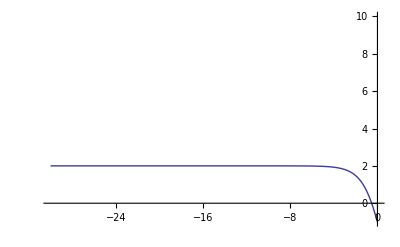

```mathematica
Plot[{h(x)=ⅇ^(2x)-4 ⅇ^x+2  }, {x, -30, 0}, PlotRange->{-1, 10}]
```

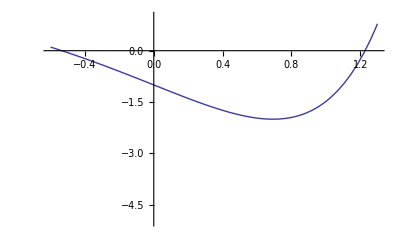

```mathematica
Plot[{h(x)=ⅇ^(2x)-4 ⅇ^x+2  }, {x, -0.6, 1.3}, PlotRange->{-5, 1}]
```

```mathematica
Plot[{h(x)=ⅇ^(2x)-4 ⅇ^x+2  }, {x, 69.98, 70}, PlotRange->{6.3*10^60, 6.34*10^60}]
```

-Graphics-

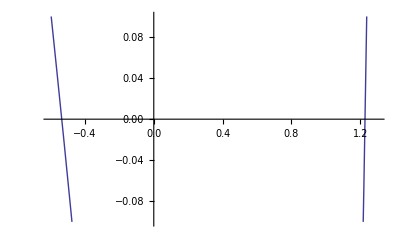

```mathematica
Plot[{h(x)=ⅇ^(2x)-4 ⅇ^x+2  }, {x, -0.6, 1.3}, PlotRange->{-0.1, 0.1}]
```

4.

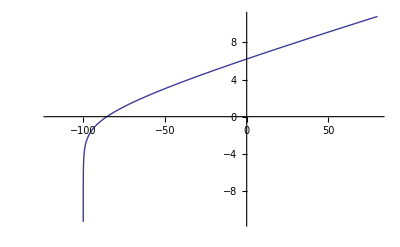

```mathematica
Plot[Log[5x+500]+x/20, {x, -120, 80}]
```

This graph shows the overview of the function.

```mathematica
Limit[Log[5x+500]+x/20, x-> ∞]
Limit[Log[5x+500]+x/20, x-> -∞]
```

∞

-∞

End Behavior: As x approaches negative infinity, y approaches negative infinity as well. As x approaches positive infinity, y approaches infinity. So, there are no horizontal asymptotes.

```mathematica
x=0;
Solve[Log[5x+500]+x/20==y, y]
NSolve[Log[5x+500]+x/20==y, y]
```

{{y→Log[500]}}

{{y→6.21461}}

The y-intercept is at (0, ln(500)) which is about (0, 6.21).

```mathematica
FindRoot[Log[5x+500]+x/20, {x, -85}]
```

{0→-85.5721}

The x-intercept is at about (-85.6, 0). -85.6 is a root.

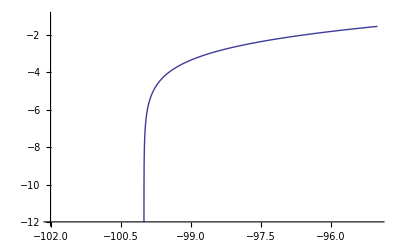

```mathematica
Plot[Log[5x+500]+x/20, {x, -102, -95}, PlotRange -> {-12, -1}]
```

As seen in this graph, there is a vertical asymptote at x= -100. This makes sense because the natural log is only defined for positive numbers, and all numbers greater than -100 make the expression inside the log positive. The x/20term of the function stretches the graph along a line of slope 1/20.

5.

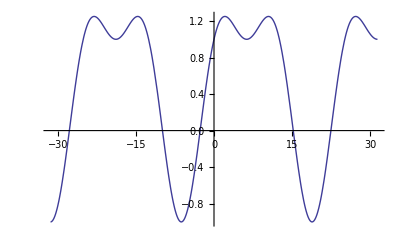

```mathematica
Plot[Cos[x/4]^2+ Sin[x/4], {x, -10Pi, 10Pi}]
```

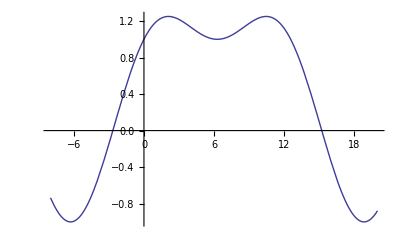

```mathematica
Plot[Cos[x/4]^2+ Sin[x/4], {x, -8, 20}]
```

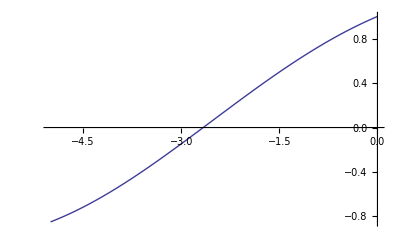

```mathematica
Plot[Cos[x/4]^2+ Sin[x/4], {x, -5, 0}]
```

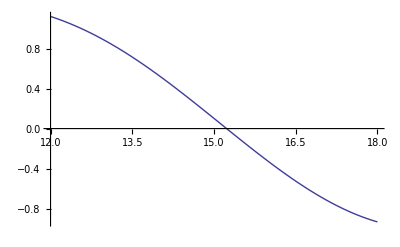

```mathematica
Plot[Cos[x/4]^2+ Sin[x/4], {x, 12, 18}]
```

6.

```mathematica
Clear[x];
Solve[0==4 x^3 -3 x^2-3x+7, x]
```

{{x→1/4 (1-5/(49-2 √569)^(1/3)-(49-2 √569)^(1/3))},{x→1/4+(5 (1+ⅈ √3))/(8 (49-2 √569)^(1/3))+1/8 (1-ⅈ √3) (49-2 √569)^(1/3)},{x→1/4+(5 (1-ⅈ √3))/(8 (49-2 √569)^(1/3))+1/8 (1+ⅈ √3) (49-2 √569)^(1/3)}}

```mathematica
N[1/4 (1-5/(49-2 √569)^(1/3)-(49-2 √569)^(1/3))]
```

-1.16985

There are three solutions to the equation given, one of which is real. This makes sense vecause the polynomial is of degree 3 so it will have at most 3 solutions. The real zero is equivalent to about -1.17. This can be confirmed in the following graph.

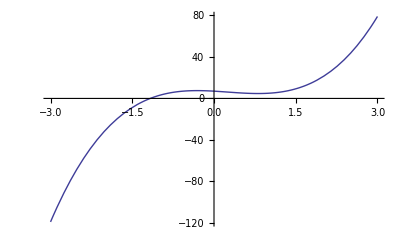

```mathematica
Plot[4 x^3 -3 x^2-3x+7, {x, -3, 3}]
```

7.

```mathematica
NSolve[0==x^5+2 x^4-302 x^3+893 x^2+1208x-3588]
```

{{x→-19.5739},{x→-2.00268},{x→1.96386},{x→3.24355},{x→14.3692}}

8.

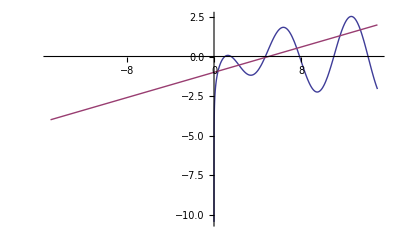

```mathematica
Plot[{Log[x]*Cos[x] , (2x)/10 - 1},{ x,-15, 15}]
```

The graph of the two sides of the equation gives us a sense of where the solutions will be within the domain given. We can find the intersection points by finding where the difference of the two functions is 0. First we zoom in on the intersection points.

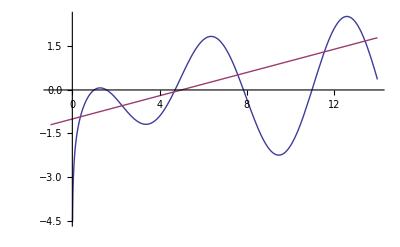

```mathematica
Plot[{Log[x]*Cos[x] , (2x)/10 - 1},{ x,-1, 14}]
```

```mathematica
FindRoot[Log[x]*Cos[x] - ((2x)/10 - 1),{x, 1}]
FindRoot[Log[x]*Cos[x] - ((2x)/10 - 1),{x, 5}]
FindRoot[Log[x]*Cos[x] - ((2x)/10 - 1),{x, 7.5}]
FindRoot[Log[x]*Cos[x] - ((2x)/10 - 1),{x, 11.5}]
FindRoot[Log[x]*Cos[x] - ((2x)/10 - 1),{x, 13.5}]
```

{x→0.370362}

{x→4.66948}

{x→7.59511}

{x→11.5614}

{x→13.4307}

So, solutions to the equation in the domain are (about) .37, 4.67, 7.60, 11.56, and 13.43.

9.

```mathematica
Factor[x^6-1]
```

(-1+x) (1+x) (1-x+x^2) (1+x+x^2)

```mathematica
Factor[x^15-1]
```

(-1+x) (1+x+x^2) (1+x+x^2+x^3+x^4) (1-x+x^3-x^4+x^5-x^7+x^8)

```mathematica
Factor[x^21-1]
```

(-1+x) (1+x+x^2) (1+x+x^2+x^3+x^4+x^5+x^6) (1-x+x^3-x^4+x^6-x^8+x^9-x^11+x^12)

```mathematica
Factor[x^55-1]
```

(-1+x) (1+x+x^2+x^3+x^4) (1+x+x^2+x^3+x^4+x^5+x^6+x^7+x^8+x^9+x^10) (1-x+x^5-x^6+x^10-x^12+x^15-x^17+x^20-x^23+x^25-x^28+x^30-x^34+x^35-x^39+x^40)

```mathematica
Factor[x^65-1]
```

(-1+x) (1+x+x^2+x^3+x^4) (1+x+x^2+x^3+x^4+x^5+x^6+x^7+x^8+x^9+x^10+x^11+x^12) (1-x+x^5-x^6+x^10-x^11+x^13-x^14+x^15-x^16+x^18-x^19+x^20-x^21+x^23-x^24+x^25-x^27+x^28-x^29+x^30-x^32+x^33-x^34+x^35-x^37+x^38-x^42+x^43-x^47+x^48)

Observed pattern: First factors out (-1+x) every time, next set of parentheses is all positive,  every set of parentheses begins with 1 +/- x, and the sum of the highest degree within each set of parentheses is equal to the degree of the factored expression. Testing examples:

```mathematica
Factor[x^32-1]
```

(-1+x) (1+x) (1+x^2) (1+x^4) (1+x^8) (1+x^16)

```mathematica
Factor[x^43-1]
```

(-1+x) (1+x+x^2+x^3+x^4+x^5+x^6+x^7+x^8+x^9+x^10+x^11+x^12+x^13+x^14+x^15+x^16+x^17+x^18+x^19+x^20+x^21+x^22+x^23+x^24+x^25+x^26+x^27+x^28+x^29+x^30+x^31+x^32+x^33+x^34+x^35+x^36+x^37+x^38+x^39+x^40+x^41+x^42)

```mathematica
Factor[x^28-1]
```

(-1+x) (1+x) (1+x^2) (1-x+x^2-x^3+x^4-x^5+x^6) (1+x+x^2+x^3+x^4+x^5+x^6) (1-x^2+x^4-x^6+x^8-x^10+x^12)

```mathematica
Factor[x^98-1]
```

(-1+x) (1+x) (1-x+x^2-x^3+x^4-x^5+x^6) (1+x+x^2+x^3+x^4+x^5+x^6) (1-x^7+x^14-x^21+x^28-x^35+x^42) (1+x^7+x^14+x^21+x^28+x^35+x^42)

10.

```mathematica
n=1;
Factor[x^(2^n)-1]
```

(-1+x) (1+x)

```mathematica
n=2;
Factor[x^(2^n)-1]
```

(-1+x) (1+x) (1+x^2)

```mathematica
n=3;
Factor[x^(2^n)-1]
```

(-1+x) (1+x) (1+x^2) (1+x^4)

```mathematica
n=4;
Factor[x^(2^n)-1]
```

(-1+x) (1+x) (1+x^2) (1+x^4) (1+x^8)

```mathematica
n=5;
Factor[x^(2^n)-1]
```

(-1+x) (1+x) (1+x^2) (1+x^4) (1+x^8) (1+x^16)

```mathematica
n=6;
Factor[x^(2^n)-1]
```

(-1+x) (1+x) (1+x^2) (1+x^4) (1+x^8) (1+x^16) (1+x^32)

So, as the pattern shows, x^(2^n)-1 can be factored as (1+x) * (1 + x^(2^n/2))(1+x^(2^n/4))(1+x^(2^n/8))... until the exponent of x is one. This can be shown by the following nested loops:

```mathematica
For[n=1, n≤6, n++, Print["\n-1+x"];For[z=2, 2^n/z≥1, z=2z, Print[1+x^(2^n/z)]]]
```

-1+x

1+x

-1+x

1+x^2

1+x

-1+x

1+x^4

1+x^2

1+x

-1+x

1+x^8

1+x^4

1+x^2

1+x

-1+x

1+x^16

1+x^8

1+x^4

1+x^2

1+x

-1+x

1+x^32

1+x^16

1+x^8

1+x^4

1+x^2

1+x

The nested loops output the factored version of x^(2^n)-1 for all n from 1 to 6. Each factor has a different line. Different groups of factors are separated by a blank line.

11.

There are 42240000 feet in 8000 miles. (5280 feet per mile.) 10 inches is 5/6 feet.

```mathematica
Solve[300000/42240000==x/(5/6)]
```

{{x→25/4224}}

```mathematica
N[25/4224]
```

0.00591856

12.

First we test our algorithm on low numbers.

```mathematica
y = N[√2,600];   (*y is set to the numberical value of √2 to 600-digit precision*)
d=2;   (*d, the decimal number we are looking for, is set to 2 for testing*)
For[x=1, x≤d, x++, y=y*10]   (*The loop multiplies √2 by 10 d number of times. A new value for y results.*)
s =ToString[AccountingForm[y]]; (*s is set to the string which conatins the accounting form of y. Accounting form prevents Mathematica from using scientific notation.*)
i = StringPosition[s,"."]; 
(*i is set to the position in the string s where the period is. Unlike in java, counting starts with 1.*)
n=Part[i-1,1,1]; (*Since i is a list of the beginning and end positions of the period (which will both be the same number), we have to extract one of those same numbers. First, we subtract one from n to get the position of the digit before the decimal. Then n is set to the first number in that list of start and end positions*)
d=ToString[d]; (*d, the decimal number we are searching for, is changed to a string for display purposes.*)
Print["decimal number "<> d<> ": " <> StringTake[s, {n, n}]] (*The result is displayed. StringTake finds the number in the digit place we found.*)
```

decimal number 2: 1

```mathematica
y = N[√2,600];   
d=7;   
For[x=1, x≤d, x++, y=y*10]   
s =ToString[AccountingForm[y]]; 
i = StringPosition[s,"."]; 
n=Part[i-1,1,1]; 
d=ToString[d]; 
Print["decimal number "<> d<> ": " <> StringTake[s, {n, n}]]
```

decimal number 7: 5

Looking below to where we print the digits of √2, we see that our answers are correct. Now we are confident with the code and will use it to find the 517th digit.

```mathematica
y = N[√2,600];   
d=517;   
For[x=1, x≤d, x++, y=y*10]   
s =ToString[AccountingForm[y]]; 
i = StringPosition[s,"."]; 
n=Part[i-1,1,1]; 
d=ToString[d]; 
Print["decimal number "<> d<> ": " <> StringTake[s, {n, n}]]
```

decimal number 517: 4

We can check this by having Mathematica show us √2to 521 digits--three extra on the end to make sure Mathematica doesn’t round, and one extra for the digit before the decimal. The fourth to last digit in the display is the 517th. It is 4. (We knew to give so many extra digits because when we gave only one extra the last two digits were 5 and 0, which indicates that the number could have been 4999.)

```mathematica
N[Sqrt[2],521]
```

1.4142135623730950488016887242096980785696718753769480731766797379907324784621070388503875343276415727350138462309122970249248360558507372126441214970999358314132226659275055927557999505011527820605714701095599716059702745345968620147285174186408891986095523292304843087143214508397626036279952514079896872533965463318088296406206152583523950547457502877599617298355752203375318570113543746034084988471603868999706990048150305440277903164542478230684929369186215805784631115966687130130156185689872372352885092648612494977

13.

```mathematica
Solve[1/1.06== x/1416.5]
```

{}

14.

```mathematica
Abs[40-4 √103]
```

-40+4 √103

-40 + 4√103 makes sense because 4 √103, about 40.6, has the greater absolute value than 40. So, the difference between the two would be 4√103-40.

15.

z=(-27)^(1/3)
z^3=-27=-27+0i=-27(Cos[0]+iSin[0]) 
r = Abs[-27]=27
arg(-27)=π, the angle in radians (For all reals the angle is either 0 or π, depending on the sign.)
2^3=-27(Cos[2kπ]+iSin[2kπ])
k=0,+-1,+-2  (Up until n-1. n=3 in this case)
2=-27^(1/3)(Cos[2 kπ/3]+iSin[2 kπ/3])

```mathematica
Clear[i]
N[-3(Cos[0]+i*Sin[0])]
N[-3(Cos[2 π/3]+i*Sin[2 π/3])]
N[-3(Cos[4 π/3]+i*Sin[4 π/3])]
```

-3.

-3. (-0.5+0.866025 i)

-3. (-0.5-0.866025 i)

These outputs are equal to -3, 1.5 - 2.5981i, and 1.5 + 2.5981i.

```mathematica
N[Factor[-27^(1/3)]]
```

1.5+2.59808 ⅈ

We can see here that Mathematica would have given us one of these answers, and the graphing calculator and our knowledge would have given us another. For the third solution we had to use DeMoivre’s formula.

16.

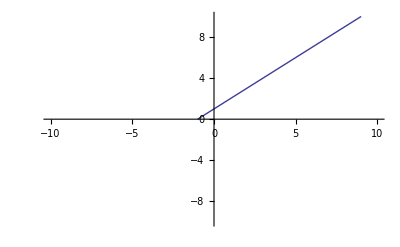

```mathematica
Plot[((x+1)^3)^(1/3),{x,-10,10},PlotRange-> {-10,10}]
```

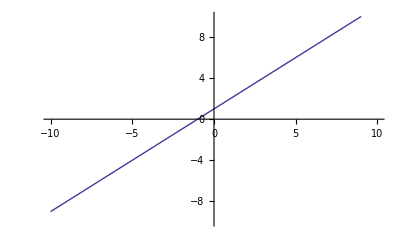

```mathematica
Plot[x+1,{x,-10,10},PlotRange-> {-10,10}]
```

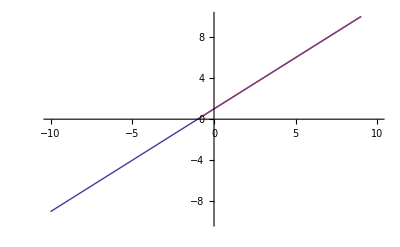

```mathematica
Plot[{x+1,((x+1)^3)^(1/3)},{x,-10,10},PlotRange-> {-10,10}]
```

The graphs overlap perfectly for the range above 0. But, the cube root graph does not show any values for negative y-values. This is because in those cases, Mathematica chooses one of the three cube roots which is not real (whereas your graphing calculator always chooses the real answer). We willl evaluate an expression to take a closer look.

```mathematica
-27.^(1/3)
```

1.5+2.59808 ⅈ

-27. is the cube of -3. But, Mathematica gives an imaginary answer.  This shows that ((-3)^3)^(1/3)is not the same as -3. So, by extension, ((x+1)^3)^(1/3)is not equal to x+1. (x could be -4, thus giving the example we just discussed.)